```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
GetData[symbol_,start_,end_]:=FinancialData["QQQ","OHLCV",{start,end}]
HedgeChart[stock_,inverse_,start_,end_]:=Module[{s1,s2,portfolio},
s1=NormalizeData[stock,start,end];
s2=NormalizeData[inverse,start,end];
portfolio=Transpose@{s2[[All,1]],Mean/@Transpose@{s1[[All,2]],s2[[All,2]]}};
DateListPlot[{s1,s2,portfolio},PlotLegends->{stock,inverse,stock<>" & "<>inverse},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[2,"Months"]];
end=Today
```

Day: Sun 29 Jul 2018

```mathematica
qqq=GetData["QQQ",start,end];
ohlcv=qqq[[All,2]];
volume=ohlcv[[All,5]];
normalizedvolume=ohlcv[[All,5]]//#/Max[#]&//N;
close=ohlcv[[All,4]];
low=ohlcv[[All,3]];
high=ohlcv[[All,2]];
daycount=20;
daycount2=14;
mean=MovingAverage[close,daycount];
std=MovingMap[StandardDeviation,close,Quantity[daycount,"Events"]];
```

```mathematica
(* average true range *)
tr0=high-low;
tr1={0}~Join~Abs[high[[2;;]]-close[[;;Length@close-1]]];
tr2={0}~Join~Abs[close[[;;Length@close-1]]-low[[2;;]]];
tr=Max/@Transpose@{tr0,tr1,tr2};
atr=MovingAverage[tr,daycount2];
```

```mathematica
(* money flow index *)
tp=Mean/@Transpose@{high,low,close};
moneyflow=tp*volume
```

{6.9642×10^9,3.85229×10^9,6.07476×10^9,7.84028×10^9,3.558×10^9,4.3284×10^9,4.38884×10^9,6.91567×10^9,5.53508×10^9,3.90245×10^9,3.953×10^9,6.66803×10^9,6.36898×10^9,8.77231×10^9,5.56839×10^9,6.70086×10^9,5.85742×10^9,7.66453×10^9,5.27663×10^9,1.336×10^10,6.71588×10^9,9.03483×10^9,7.92226×10^9,6.26183×10^9,5.45724×10^9,4.37866×10^9,5.45035×10^9,6.46796×10^9,4.83615×10^9,4.23672×10^9,5.3424×10^9,4.99018×10^9,5.03782×10^9,3.83876×10^9,5.56751×10^9,4.17782×10^9,5.57342×10^9,6.43883×10^9,3.97062×10^9,6.66554×10^9,6.5565×10^9,7.36785×10^9,1.06135×10^10}

```mathematica
sign=(tp[[2;;]]-tp[[;;Length@tp-1]])//If[#>0,1,If[#<0,-1,0]]&
```

If[{1.01,0.34,1.85,1.75333,0.775,0.618333,-0.66,-0.4699,0.676567,0.753333,0.533333,1.2,-0.525,-0.775,-0.78,2.04333,-0.973333,-0.860333,-3.73633,0.442833,-1.19283,-0.263333,1.27833,-0.215,-0.146667,0.71,2.44667,1.96333,0.503333,-0.82,2.23667,0.82,-0.15,0.0633333,0.516667,-0.673333,0.0733333,-0.336667,1.65667,1.37667,-1.75333,-1.75}>0,1,If[{1.01,0.34,1.85,1.75333,0.775,0.618333,-0.66,-0.4699,0.676567,0.753333,0.533333,1.2,-0.525,-0.775,-0.78,2.04333,-0.973333,-0.860333,-3.73633,0.442833,-1.19283,-0.263333,1.27833,-0.215,-0.146667,0.71,2.44667,1.96333,0.503333,-0.82,2.23667,0.82,-0.15,0.0633333,0.516667,-0.673333,0.0733333,-0.336667,1.65667,1.37667,-1.75333,-1.75}<0,-1,0]]

```mathematica
sign=If[#>0,1,If[#<0,-1,0]]&/@(tp[[2;;]]-tp[[;;Length@tp-1]])
```

{1,1,1,1,1,1,-1,-1,1,1,1,1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,1,-1,-1,1,1,1,1,-1,1,1,-1,1,1,-1,1,-1,1,1,-1,-1}

```mathematica
sign//Length
```

42

```mathematica
moneyflow//Length
```

43

```mathematica
high-low
```

{1.96,1.26,1.57,1.97,1.27,1.065,1.75,2.38,1.7003,1.06,1.04,1.71,1.39,1.215,1.71,2.33,1.33,2.51,1.679,4.18,1.6885,3.97,2.6,1.525,3.18,2.82,2.03,2.74,1.41,1.01,1.27,2.38,0.95,1.07,3.37,1.06,1.06,1.38,1.9,2.49,2.64,1.11,4.71}

```mathematica
mean2=MovingMap[Mean,close,Quantity[daycount,"Events"]];
```

```mathematica
high[[2;;]]//Length
```

42

```mathematica
low[[2;;]]//Length
```

42

```mathematica
std//Length
```

24

```mathematica
mean2//Length
```

24

```mathematica
std//Length
```

24

```mathematica
close//Length
```

43

```mathematica
mean
```

{174.456,174.611,174.589,174.645,174.59,174.515,174.313,174.166,174.225,174.363,174.483,174.513,174.695,174.795,174.905,175.094,175.29,175.379,175.543,175.755,176.202,176.739,177.255,177.577}

```mathematica
mean2
std
```

{174.456,174.611,174.589,174.645,174.59,174.515,174.313,174.166,174.225,174.363,174.483,174.513,174.695,174.795,174.905,175.094,175.29,175.379,175.543,175.755,176.202,176.739,177.255,177.577}

{2.50396,2.22714,2.276,2.17029,2.2334,2.26856,2.41335,2.40368,2.42489,2.51405,2.59803,2.61741,2.83095,2.9717,3.095,3.30494,3.47417,3.54902,3.63974,3.74794,3.72994,3.87498,3.56743,3.26937}

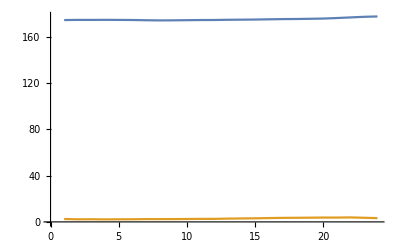

```mathematica
ListLinePlot[{mean,std}]
```

```mathematica
data=NormalizeData["QQQ",start,end];
daycount=20;
```

```mathematica
volatility=MovingMap[StandardDeviation,data,Quantity[daycount,"Events"]];
max0=MovingMap[Max,data,Quantity[daycount,"Events"]];
min0=MovingMap[Min,data,Quantity[daycount,"Events"]];
```

19

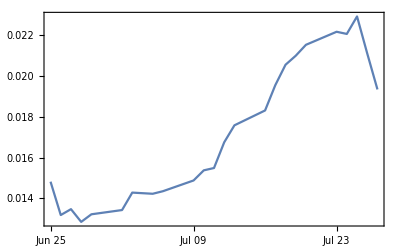

```mathematica
Length@data-Length@max0
DateListPlot[volatility]
```

```mathematica
max=Transpose[{Take[data[[All,1]],Length@max0],max0[[All,2]]}];
min=Transpose[{Take[data[[All,1]],Length@min0],min0[[All,2]]}];
```

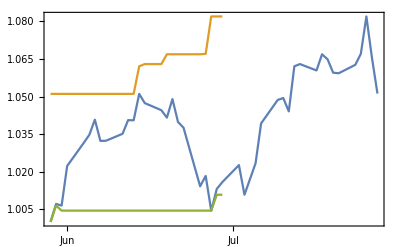

```mathematica
DateListPlot[{data,max,min}]
```

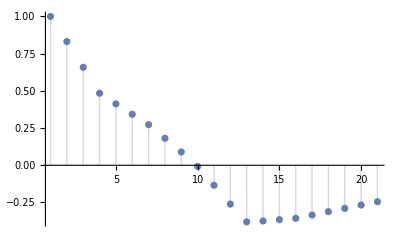

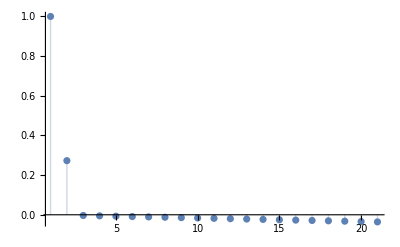

```mathematica
ListPlot[CorrelationFunction[max[[All,2]],{daycount}],Filling->Axis,PlotRange->All]
ListPlot[CorrelationFunction[min[[All,2]],{daycount}],Filling->Axis,PlotRange->All]
```

```mathematica
modelmax=TimeSeriesModelFit[max[[All,2]]];
modelmin=TimeSeriesModelFit[min[[All,2]]];
```

```mathematica
future=Range[Length@max+1,Length@max+daycount-1]
```

{25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

```mathematica
forecastmax=modelmax/@future;
forecastmin=modelmin/@future;
```

```mathematica
forecastmax//Length
```

19

```mathematica
forecastmax
```

{1.08465,1.086,1.08734,1.08868,1.09003,1.09137,1.09271,1.09406,1.0954,1.09674,1.09809,1.09943,1.10077,1.10211,1.10346,1.1048,1.10614,1.10749,1.10883}

```mathematica
lastday=First@Last@max;
futuredates=DateRange[DayPlus[lastday,1,"BusinessDay"],DayPlus[lastday,daycount-2,"BusinessDay"],"BusinessDay"]//DateList/@#&
```

{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}

```mathematica
upper=TimeSeries[forecastmax,{futuredates}]
lower=TimeSeries[forecastmin,{futuredates}]
```

TemporalData::tpspc: The time specification {{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}} should be one of Automatic, a time range, a list containing a list of explicit times, or a list containing one such specification for each path in the data.

TimeSeries[{1.08465,1.086,1.08734,1.08868,1.09003,1.09137,1.09271,1.09406,1.0954,1.09674,1.09809,1.09943,1.10077,1.10211,1.10346,1.1048,1.10614,1.10749,1.10883},{{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}}]

TemporalData::tpspc: The time specification {{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}} should be one of Automatic, a time range, a list containing a list of explicit times, or a list containing one such specification for each path in the data.

TimeSeries[{1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492},{{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}}]

```mathematica
DateListPlot[{data,max,min,lower,upper},Joined->True,PlotTheme->"Detailed",Joined->True]
```

DateListPlot::ldata: {{{{2018,5,29},1.},{{2018,5,30},1.00716},{{2018,5,31},1.00651},{{2018,6,1},1.02231},{{2018,6,4},1.03154},{{2018,6,5},1.03474},«32»,{{2018,7,23},1.06267},{{2018,7,24},1.06705},{{2018,7,25},1.08197},{{2018,7,26},1.06557},{{2018,7,27},1.05119}},«3»,«1»} is not a valid dataset or list of datasets.

DateListPlot[{{{{2018,5,29},1.},{{2018,5,30},1.00716},{{2018,5,31},1.00651},{{2018,6,1},1.02231},{{2018,6,4},1.03154},{{2018,6,5},1.03474},{{2018,6,6},1.04078},{{2018,6,7},1.03231},{{2018,6,8},1.03237},{{2018,6,11},1.03515},{{2018,6,12},1.0406},{{2018,6,13},1.04054},{{2018,6,14},1.05107},{{2018,6,15},1.0474},{{2018,6,18},1.04456},{{2018,6,19},1.04161},{{2018,6,20},1.049},{{2018,6,21},1.03989},{{2018,6,22},1.03758},{{2018,6,25},1.0142},{{2018,6,26},1.01835},{{2018,6,27},1.0045},{{2018,6,28},1.01314},{{2018,6,29},1.01586},{{2018,7,2},1.02267},{{2018,7,3},1.01083},{{2018,7,5},1.02338},{{2018,7,6},1.0393},{{2018,7,9},1.04865},{{2018,7,10},1.04942},{{2018,7,11},1.04409},{{2018,7,12},1.06208},{{2018,7,13},1.06297},{{2018,7,16},1.06042},{{2018,7,17},1.06688},{{2018,7,18},1.06486},{{2018,7,19},1.05954},{{2018,7,20},1.0593},{{2018,7,23},1.06267},{{2018,7,24},1.06705},{{2018,7,25},1.08197},{{2018,7,26},1.06557},{{2018,7,27},1.05119}},{{{2018,5,29},1.05107},{{2018,5,30},1.05107},{{2018,5,31},1.05107},{{2018,6,1},1.05107},{{2018,6,4},1.05107},{{2018,6,5},1.05107},{{2018,6,6},1.05107},{{2018,6,7},1.05107},{{2018,6,8},1.05107},{{2018,6,11},1.05107},{{2018,6,12},1.05107},{{2018,6,13},1.05107},{{2018,6,14},1.06208},{{2018,6,15},1.06297},{{2018,6,18},1.06297},{{2018,6,19},1.06688},{{2018,6,20},1.06688},{{2018,6,21},1.06688},{{2018,6,22},1.06688},{{2018,6,25},1.06688},{{2018,6,26},1.06705},{{2018,6,27},1.08197},{{2018,6,28},1.08197},{{2018,6,29},1.08197}},{{{2018,5,29},1.},{{2018,5,30},1.00651},{{2018,5,31},1.0045},{{2018,6,1},1.0045},{{2018,6,4},1.0045},{{2018,6,5},1.0045},{{2018,6,6},1.0045},{{2018,6,7},1.0045},{{2018,6,8},1.0045},{{2018,6,11},1.0045},{{2018,6,12},1.0045},{{2018,6,13},1.0045},{{2018,6,14},1.0045},{{2018,6,15},1.0045},{{2018,6,18},1.0045},{{2018,6,19},1.0045},{{2018,6,20},1.0045},{{2018,6,21},1.0045},{{2018,6,22},1.0045},{{2018,6,25},1.0045},{{2018,6,26},1.0045},{{2018,6,27},1.0045},{{2018,6,28},1.01083},{{2018,6,29},1.01083}},TimeSeries[{1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492,1.00492},{{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}}],TimeSeries[{1.08465,1.086,1.08734,1.08868,1.09003,1.09137,1.09271,1.09406,1.0954,1.09674,1.09809,1.09943,1.10077,1.10211,1.10346,1.1048,1.10614,1.10749,1.10883},{{{2018,7,2,0,0,0.},{2018,7,3,0,0,0.},{2018,7,5,0,0,0.},{2018,7,6,0,0,0.},{2018,7,9,0,0,0.},{2018,7,10,0,0,0.},{2018,7,11,0,0,0.},{2018,7,12,0,0,0.},{2018,7,13,0,0,0.},{2018,7,16,0,0,0.},{2018,7,17,0,0,0.},{2018,7,18,0,0,0.},{2018,7,19,0,0,0.},{2018,7,20,0,0,0.},{2018,7,23,0,0,0.},{2018,7,24,0,0,0.},{2018,7,25,0,0,0.},{2018,7,26,0,0,0.}}}]},Joined→True,PlotTheme→Detailed,Joined→True]